# Quad Prog min 0.5 x.G.x+c.x A_e.x=b_e and A_i.x≥b_i

16.1 did the theory of solving the equality constrained problem by introducing the KKT matrix. 16.2 discusses directly solving the KKT system by factorizing and the Schur complement. 16.3 discusses iterative solvers for the KKT system. 16.4 introduces inequality constraints. 16.5 Discusses Active Set methods. 16.6 introduces interior point methods.

In this notebook I am going to demo building and solving the KKT matrix, discuss the drawbacks of Active Set methods, and demo interior point methods.

## 16.1,2,3 KKT Matrix for min 0.5 x.G.x+c.x A_e.x=b_e

The solution of the equality constrained optimization problem is x where
	(G | -Aᵀ
A | 0).(x
λ)=(-c
  b) 
The vector of Lagrange multipliers λ does not have any sign conditions.

Equivalently the solution of the equality constrained optimization problem is x=x_0+p where
	(G | Aᵀ
A | 0).(-p
λ)=(G.x_0+c
  A.x_0-b) 
As before, the vector of Lagrange multipliers λ does not have any sign conditions.

The matrix 
	(G | Aᵀ
A | 0)
is called the KKT matrix.

Here is the first form in action

```mathematica
{m,n}={16,14};
G=RandomReal[{-1,1},{m,m}];G=G+Gᵀ;
c=RandomReal[{-1,1},m];
A=RandomReal[{-1,1},{n,m}];
b=RandomReal[{-1,1},n];
KKT=ArrayFlatten[({{G, -Aᵀ}, {A, 0}})];
Eigenvalues[ArrayFlatten[({{G, Aᵀ}, {A, 0}})]]
KKTRHS=Join[-c,b];
xλ=LinearSolve[KKT,KKTRHS];
{x,λ}={xλ⟦1;;m⟧,xλ⟦m+1;;m+n⟧};
Map[Norm,{A.x-b, G.x+c-Aᵀ.λ}]
```

{7.82675,6.55466,5.82032,-5.52097,4.95515,-4.77919,-4.5261,4.13601,-3.81051,-3.56557,3.24436,-3.05071,3.01454,-2.64869,2.49486,-2.35039,1.95146,1.9272,-1.78092,1.34912,-1.15587,1.1459,-0.804842,0.736044,0.543225,-0.476361,0.427278,-0.398781,-0.216343,0.0320475}

{2.55072×10^-14,2.37442×10^-14}

## 16.4 KKT Conditions for min 0.5 x.G.x+c.x A_e.x=b_e and A_i.x≥b_i

Writing λ_e for the Lagrange multipliers for the equality constraints and λ_i for the Lagrange multipliers for the inequality constraints we get the KKT conditions 
	G.x+c-(A_e)ᵀ.λ_e-(A_i)ᵀ.λ_i=0
with 
	A_e.x | = | b_e
A_i.x | ≥ | b_i
λ_i | ≥ | 0 
The vector of Lagrange multipliers λ_e for the equality constraints does not have any sign conditions.

## 16.5 Active Set methods of min 0.5 x.G.x+c.x A_e.x=b_e and A_i.x≥b_i

Active set methods work by appending inequality constraints to the equality constraints in a systematic manner.  The key observation is that if we knew which of the inequality constraints were active at the solution we could ignore the inactive inequality constraints and simply solve the KKT system with the active constraints.  The problem is that we do not know which constraints are active at the solution. Active set methods trek along the border of the feasible region switching constraints of and on at corners and/or when the multiplier violate sign conditions.  They involve a lot of book keeping. They are no longer competitive since the development of interior point methods.

## 16.6 Interior Point methods for min 0.5 x.G.x+c.x A.x≥b

For now consider G SPD.  Our KKT conditions are 
	G.x-Aᵀ.λ+c | = | 0_m
A.x-b | ≥ | 0_n
(A.x-b)∘λ | = | 0_n
λ | ≥ | 0_n
Equations are better than inequalities so we introduce the vector of slack variables
	y=A.x-b≥0_n
so that we have 
 	G.x-Aᵀ.λ+c | = | 0_m
A.x-y-b | = | 0_n
y∘λ | = | 0_n
λ | ≥ | 0
y | ≥ | 0
 Not surprisingly, the algorithm is iterative.  For a feasible triple (x,y,λ) define the “complementary measure”
 	μ=(y.λ)/m
 and consider the perturbed KKT conditions
 	F[{x,y,λ};σ μ]:=(G.x-Aᵀ.λ+c
A.x-y-b
Y.Λ.e-σ μ e)=(0_m
0_n
0_n)
 where the diagonal matrices Y and Λ have the vectors y and λ on their diagonals, the vector e={1,1,…,1}, and the scalar σ satisfies 0≤σ≤1. If we fix μ a Newton step from a feasible iterated 
 	{x_k,y_k,λ_k}	
 for the nonlinear system is computed by solving 
 	(G | 0 | -Aᵀ
A | -I_n | 0
0 | Λ | Y).(Δx
Δy
Δλ)=(-r_d
-r_p
-Λ.Y.e+σ μ e)=(G.x-Aᵀ.λ+c
A.x-y-b
Δλ)
 The  next iterate “should” be
 	{x^+,y^+,λ^+}={x_k,y_k,λ_k}+{Δx,Δy,Δλ}
 The problem is that this may violate the conditions
 	y^+≥0 and/or λ^+≥0.
 The next iterate is chosen with a line search 
 	{x_(k+1),y_(k+1),λ_(k+1)}={x_k,y_k,λ_k}+α{Δx,Δy,Δλ}
 where α∈(0,1) ensures the next point is feasible! In linear programming different step lengths are frequently chosen for the primal (x and y) and dual (λ) variables i.e. the update is  
 	{x_(k+1),y_(k+1),λ_(k+1)}={x_k,y_k,λ_k}+α_p{Δx,Δy,0}+α_d{0,0,Δλ}
 This is not always such a good idea in quadratic programming. A common choice of a single α is the largest value that preserves all the required sign conditions.

## 16.6 Interior Point method Implementation Algorithm 16.4 p484/506 min 0.5 x.G.x+c.x A.x≥b

Initialize with feasible point (x_0,y_0,λ_0) i.e. y_0=A.x_0-b≥0_n and λ_0≥0_n

Iterate “to convergence” k=0,1,2,3,…

(x,y,λ)=(x_k,y_k,λ_k) and solve (16.58) with σ=0 to get (Δx^aff,Δy^aff,Δλ^aff).

Calculate μ=(y.λ)/m

Calculate (α̂)_aff=Max[0≤a≤1: (y,λ)+α(Δy^aff,Δλ^aff)≥0]

Calculate μ_aff=((y +  (α̂)_aff Δy^aff).(λ + (α̂)_aff Δλ^aff))/m

Set σ=(μ_aff/μ)^3

Solve 16.67 for (Δx,Δy,Δλ)

Choose τ_k∈(0,1) and set α̂=min(α_τ_k^pri,α_τ_k^dual) (see 16.66)

Update (x_k,y_k,λ_k)=(x_k,y_k,λ_k)+α̂(Δx,Δy,Δλ)

There is quite a lot of stuff to be defined and explained here! First
	(16.58) (G | 0 | -Aᵀ
A | -I | 0
0 | Λ | Y).(Δx
Δy
Δλ)=(-r_d
-r_p
-Λ.Y.e+σ μ e)=(-(G.x-Aᵀ.λ+c)
-(A.x-y-b))
-Λ.Y.e+σ μ e)
is just the Newton step.  Step 2.2 just estimates how far from “complementarity” the original point is. Step 2.3 works out how far you can go in the affine “Newton” direction and maintain feasibility.  Step 2.4 checks how far from “complementarity” the new trial point is.  Step 2.5 computes a new value for σ from the two complementarity gaps. Step 2.6 uses that σ in the Newton Step with the affine Λ and Y
	(16.67) (G | 0 | -Aᵀ
A | -I | 0
0 | Λ | Y).(Δx
Δy
Δλ)=(-r_d
-r_p
-(Λ.Y+ΔΛ^aff ΔY^aff)e+σ μ e)=(-(G.x-Aᵀ.λ+c)
-(A.x-y-b))
-(Λ.Y+ΔΛ^aff ΔY^aff)e+σ μ e)
Step 2.7 chooses maximum primal and dual steps sizes with the same safety factor τ
	(16.66) 	 α_τ^pri | = | Max[0≤α≤1:y+α Δy≥(1-τ)y]
α_τ^dual | = | Max[0≤α≤1:λ+α Δλ≥(1-τ)λ]
The Min ensures that both the updated slack variables y and updated Lagrange multipliers λ satisfy the feasibility conditions y+α̂ Δy≥0 and λ+α̂ Δλ≥0.  All of this manipulation is motivated by experience in the linear programming case and is designed to ensure that the “Newton” steps maintain feasibility.

## 16.XX Some unfortunate Active Set Behavior: An argument for staying off the constraints

Suppose our constraints are a linearization of the constraint 
	G[{x1,x2}]=1-(x_1^2+x_2^2)≥0  
At a point p on the boundary my linearized constraints are 
	G[p]+∇G(p).(x-p)=∇G(p).(x-p)=2p(x-p)≥0
My linearized set and the original set looks like this

```mathematica
G[{x1_,x2_}]:=1-(x1^2+x2^2)≥0
LCons[n_][{x1_,x2_}]:=Module[{p,grad},
Apply[And,Table[ 
p={Cos[θ],Sin[θ]};
-2p.({x1,x2}-p)≥0,
{θ,2.π/n, 2π,2π/n}]]
]
TabView[
Map[
RegionPlot[#[{x1,x2}],{x1,-1.4,1.4},{x2,-1.4,1.4},Epilog->{Red,Circle[{0,0},1]}]&,
Table[LCons[i],{i,1,20}]],6]
```

1234567891011121314151617181920

In this simple low-dimensional case, active set methods have a bad habit of stepping around this simple polygon one corner at a time! It is worse in higher dimensions because there are a lot of corners and edges in higher dimensions.

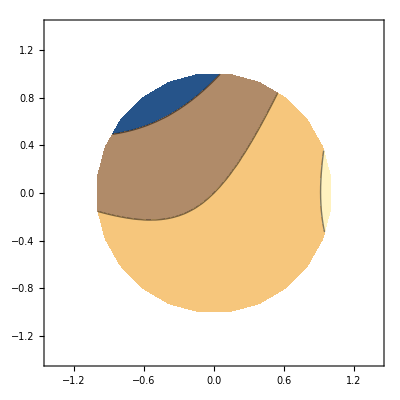

```mathematica
m=2; G=RandomReal[{-1,1},{m,m}]; c=RandomReal[{-1,1},m];
ContourPlot[0.5 {x1,x2}.G.{x1,x2} +c.{x1,x2},
{x1,-1.4,1.4},{x2,-1.4,1.4},
RegionFunction->Function[{x1,x2},LCons[24][{x1,x2}]]
]
```

In the presence of a lot of “poorly understood” constraints interior point methods are believed to have a significant advantage.

## 16.XX Active Set Advantage There is a potential advantage for Active Set tracking if you have a good initial guess for which constraints are important. Sometimes the case with a slowly changing system.